```mathematica
Quit
```

```mathematica
NotebookDirectory[]
```

/Users/esser/Documents/PROJECTS/ALPsPheno/ALP multibosons/notebooks/

## Fit the cross section as a polynomial in C_B and C_W

```mathematica
(* list (CB, CW, sigma)*)
VBFsigma = {{-1,1, 0.02754},{0,1,0.005774},{1,1,0.005672 }, {-1,-1, 0.005566}, {0,-1,0.00579 },{1,-1,0.02753}, {-1,0, 0.001014}, {0,0,0}, {1,0, 0.001018}, {0,2,0.09295}, {0.5, 1, 0.003394},{-0.5, 1, 0.01313}, {1,0.5,0.001871}, {1,-0.5,0.005791},{-0.1,0.1, 2.754*10^-06}};
```

```mathematica
Fit[VBFsigma,{CB^4,CB^3 *CW, CB^2*CW^2, CB*CW^3, CW^4},{CB,CW}]
```

0.00102865 CB^4-0.00160019 CB^3 CW+0.00973456 CB^2 CW^2-0.00935486 CB CW^3+0.00580889 CW^4

```mathematica
sigmaVBF[CB_,CW_]:=0.0010286470032311028 CB^4-0.0016001897983539096 CB^3 CW+0.009734562945808179 CB^2 CW^2-0.009354856465020562 CB CW^3+0.0058088939579702915 CW^4
```

```mathematica
sigmaVBF[-0.1,0.1]
```

2.75272×10^-6

```mathematica
Fit[VBFsigma,{CB^4, CB^2*CW^2, CW^4},{CB,CW}]
```

0.00102865 CB^4+0.00973456 CB^2 CW^2+0.00580889 CW^4

```mathematica
sigmaVBFnoCross[CB_,CW_]:=0.0010286470009428926 CB^4+0.009734562974059667 CB^2 CW^2+0.005808893957937185 CW^4
```

```mathematica
sigmaVBFnoCross[0.1,0.1]
```

1.65721×10^-6

```mathematica
sigmaVBF[0,1]*0.0673*1000
```

0.390939

## pT of the photon for γZ

```mathematica
data ={5.9000*10^-02,2.6400*10^-02,7.4000*10^-03,1.4700*10^-03};
```

```mathematica
dataUnc = {2.1000*10^-02,6.0000*10^-03,2.4000*10^-03,6.8000*10^-04};
```

```mathematica
background ={5.3900*10^-02,1.3400*10^-02,4.9000*10^-03,1.1400*10^-03};
```

```mathematica
signal0={6.4582*10^-04,1.0708*10^-03,7.7807*10^-04,2.8399*10^-04};
```

```mathematica
binCenter={50,100,160,300};
```

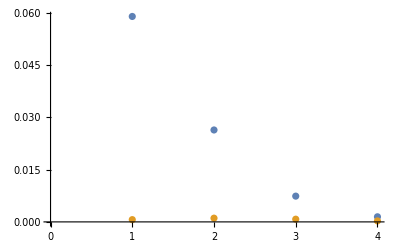

```mathematica
ListPlot[{data,signal0}]
```

```mathematica
s2th = 0.22305;
c2th = 1- s2th;
```

```mathematica
Nevents[CB_, CW_]:=background+signal0*sigmaVBF[CB,CW]/sigmaVBF[0,1];
```

```mathematica
chi2[CB_, CW_]:=Sum[((data[[i]]-Nevents[CB,CW][[i]])/dataUnc[[i]])^2,{i,0,Length[data]}];
```

```mathematica
chi2min=FindMinimum[chi2[CB,CW],{{CB,0},{CW,0}}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{6.074,{CB→0.,CW→0.}}

```mathematica
chi2bin= Table[(((data[[i]]-Nevents[CB,CW][[i]])/dataUnc[[i]])^2-chi2min[[1]]/Length[data])/(chi2[CB,CW]-chi2min[[1]]),{i,1,Length[data]}];
```

```mathematica
Length[chi2bin]
```

4

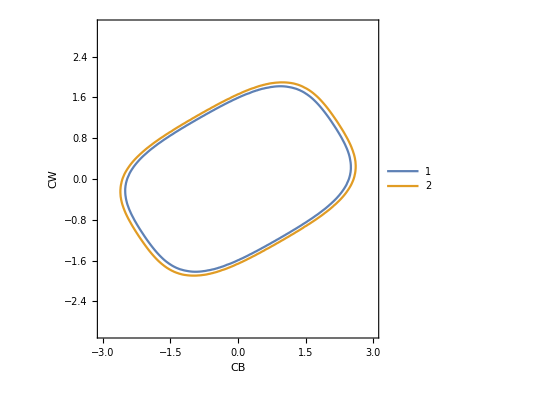

```mathematica
ContourPlot[{chi2[CB,CW]-chi2min[[1]]==1,chi2[CB,CW]-chi2min[[1]]==4},{CB,-3,3},{CW,-3,3} ,FrameLabel->(Style[#,14,Bold]&/@{CB,CW}),PlotLegends->Automatic]
```

```mathematica
chi2[0,-1.10]
```

4.007

```mathematica
Solve[chi2[0,CW]==4,CW]
```

{{CW→-1.45753},{CW→-1.10138},{CW→0.-1.10138 ⅈ},{CW→0.+1.10138 ⅈ},{CW→0.-1.45753 ⅈ},{CW→0.+1.45753 ⅈ},{CW→1.10138},{CW→1.45753}}

```mathematica
Solve[chi2[CB,0]==4,CB]
```

{{CB→-2.24685},{CB→-1.69783},{CB→0.-1.69783 ⅈ},{CB→0.+1.69783 ⅈ},{CB→0.-2.24685 ⅈ},{CB→0.+2.24685 ⅈ},{CB→1.69783},{CB→2.24685}}

The individual 2σ limits are CW=1.46and CB=2.25 for the respective other WC zero.

Plot the χ^2 per bin minus the averaged χ^2per bin (i.e. χ^2/number of bins) and normalise by the total χ^2-(χ^2)_min:

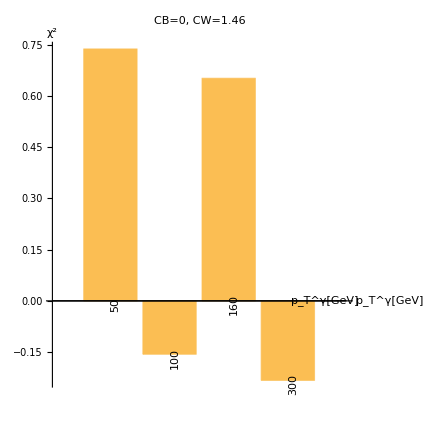

```mathematica
BarChart[chi2bin/.{CB->0, CW->1.46},ChartLabels->Placed[binCenter,Below,Rotate[#,90 Degree]&], AxesLabel->{"p_T^γ[GeV]", "χ^2"},PlotLabel->"CB=0, CW=1.46",AspectRatio->1]
```

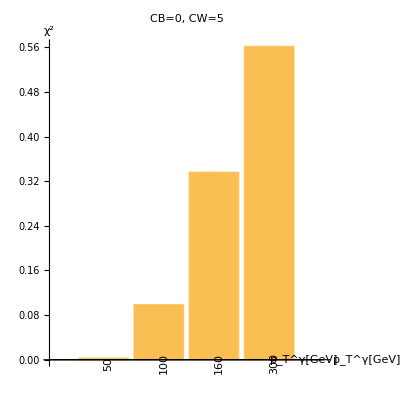

```mathematica
BarChart[chi2bin/.{CB->0, CW->5},ChartLabels->Placed[binCenter,Below,Rotate[#,90 Degree]&], AxesLabel->{"p_T^γ[GeV]", "χ^2"},PlotLabel->"CB=0, CW=5",AspectRatio->1]
```

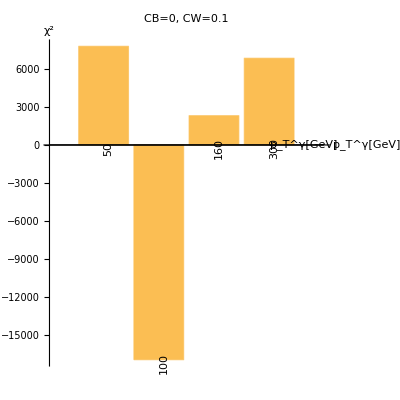

```mathematica
BarChart[chi2bin/.{CB->0, CW->0.1},ChartLabels->Placed[binCenter,Below,Rotate[#,90 Degree]&], AxesLabel->{"p_T^γ[GeV]", "χ^2"},PlotLabel->"CB=0, CW=0.1",AspectRatio->1]
```

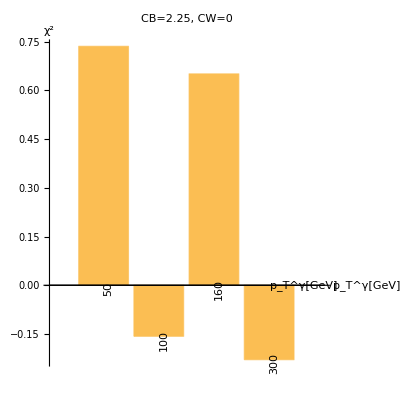

```mathematica
BarChart[chi2bin/.{CB->2.25, CW->0},ChartLabels->Placed[binCenter,Below,Rotate[#,90 Degree]&], AxesLabel->{"p_T^γ[GeV]", "χ^2"},PlotLabel->"CB=2.25, CW=0",AspectRatio->1]
```

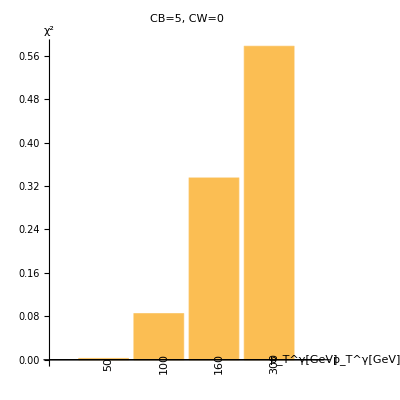

```mathematica
BarChart[chi2bin/.{CB->5, CW->0},ChartLabels->Placed[binCenter,Below,Rotate[#,90 Degree]&], AxesLabel->{"p_T^γ[GeV]", "χ^2"},PlotLabel->"CB=5, CW=0",AspectRatio->1]
```

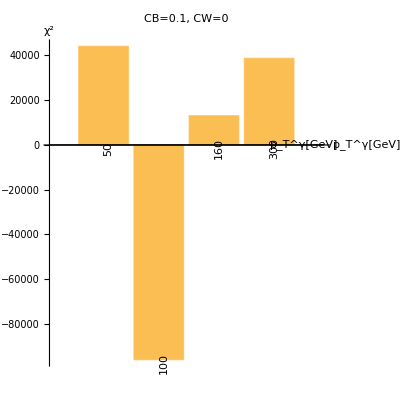

```mathematica
BarChart[chi2bin/.{CB->0.1, CW->0},ChartLabels->Placed[binCenter,Below,Rotate[#,90 Degree]&], AxesLabel->{"p_T^γ[GeV]", "χ^2"},PlotLabel->"CB=0.1, CW=0",AspectRatio->1]
```

## pT of the leading jet

```mathematica
dataLj ={1.9000*10^-02,1.3300*10^-02,5.6000*10^-03,1.0900*10^-03};
```

```mathematica
dataUncLj = {1.0000*10^-02,2.6000*10^-03,2.5000*10^-03,3.6000*10^-03};
```

```mathematica
backgroundLj ={1.7600*10^-02,1.4900*10^-02,5.2000*10^-03,5.9000*10^-04};
```

```mathematica
signal0Lj={9.5962*10^-03,1.5910*10^-02,1.1561*10^-02,4.2197*10^-03};
```

```mathematica
binCenterLj={50,100,160,300};
```

```mathematica
ListPlot[{dataLj,signal0Lj}]
```

-Graphics-

```mathematica
s2th = 0.22305;
c2th = 1- s2th;
```

```mathematica
Nevents[CB_, CW_]:=background+signal0*sigmaVBF[CB,CW]/sigmaVBF[0,1];
```

```mathematica
chi2[CB_, CW_]:=Sum[((data[[i]]-Nevents[CB,CW][[i]])/dataUnc[[i]])^2,{i,0,Length[data]}];
```

```mathematica
chi2min=FindMinimum[chi2[CB,CW],{{CB,0},{CW,0}}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{6.074,{CB→0.,CW→0.}}

```mathematica
chi2bin= Table[(((data[[i]]-Nevents[CB,CW][[i]])/dataUnc[[i]])^2-chi2min[[1]]/Length[data])/(chi2[CB,CW]-chi2min[[1]]),{i,1,Length[data]}];
```

```mathematica
Length[chi2bin]
```

4

```mathematica
ContourPlot[{chi2[CB,CW]-chi2min[[1]]==1,chi2[CB,CW]-chi2min[[1]]==4},{CB,-3,3},{CW,-3,3} ,FrameLabel->(Style[#,14,Bold]&/@{CB,CW}),PlotLegends->Automatic]
```

-Graphics-